## Essential code

### SSS & Causal Network Construction

Build a causal network from a SSS, modeling the Sequential Substituion System using tags.  This allows us to build the SSS evolution and the causal network simultaneously.  
(Based on code from NKS, pp. 1033, and suggestions of Matthew Szudzik.)

#### Format conversion

```mathematica
Attributes[s]=Flat;
```

```mathematica
Clear[SSSConvert];
SSSConvert[string_String] := s@@(Characters[string]/.Thread[CharacterRange["A","Z"]->Range[0,25]])
SSSConvert[s[x__]] := StringJoin[{x}/.Thread[Range[0,25]->CharacterRange["A","Z"]]]
```

```mathematica
SSSConvert::usage="Converts SSS (sequential substitution system) states between s- and string-formats.";
```

```mathematica
?SSSConvert
```

Converts SSS (sequential substitution system) states between s- and string-formats.

```mathematica
SSSConvert["AABBBA"]
```

s[0,0,1,1,1,0]

```mathematica
SSSConvert[%]
```

AABBBA

#### SSSRuleIcon

```mathematica
$MaxColor=6;  (* If you want to treat SSSs with more than 6 symbols, just change this variable *)
```

```mathematica
myColors=Sequence[ColorRules->{0->LightGray},ColorFunction->(Hue[(#-1)/$MaxColor]&),ColorFunctionScaling->False];
```

```mathematica
patternPrint[pattern_,opts___] := ArrayPlot[{{##}}& @@pattern,myColors,Mesh->True,opts,ImageSize->{Automatic,20}];
```

```mathematica
Clear[SSSRuleIcon];
SSSRuleIcon[(rule_String|rule_Rule|rule_RuleDelayed),x___]:=SSSRuleIcon[{rule},x];

SSSRuleIcon[rules_List,x___]:=SSSRuleIcon[Map[SSSConvert,rules,{-1}],x] /; !FreeQ[rules,_String,Infinity];

SSSRuleIcon[rules_List,opts___] := Panel[Grid[Map[patternPrint[#,opts]&,rules,{2}] /. 
{Rule[x_,y_]:>{x,"→",y},RuleDelayed[x_,y_]:>{x,":>",y}}, (* invisible AlignmentMarkers! *)
Alignment->Left],"Substitution Rule"<>If[Length[rules]>1,"s:",":"]] /; FreeQ[rules,_String,Infinity];
```

```mathematica
SSSRuleIcon::usage="SSSRuleIcon[rule(s)] generates an icon for a sequential substitution system (SSS) rule or set of rules.";
```

```mathematica
?SSSRuleIcon
```

SSSRuleIcon[
StyleBox["rule",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"]] generates an icon for a sequential substitution system (SSS) rule or set of rules.


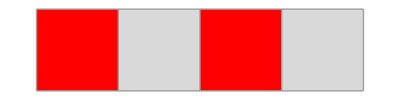
-Graphics- | → | -Graphics-Substitution Rule:

```mathematica
SSSRuleIcon["ABA"->"BABA"]
```

#### Initialization

Since we're going to have to initialize the global variables $SSSConnectionList and $SSSTagIndex anyway, let's add another: $SSSInitial

```mathematica
Clear[SSSInitialize];
SSSInitialize[string_String,mode___] := (
$SSSInitial=s@@Transpose[{#,Range[Length[#]]}& @ (Characters[string]/.Thread[CharacterRange["A","Z"]->Range[0,25]])];
$SSSConnectionList={}; 
$SSSTagIndex=StringLength[string]+1;                     (* value of next tag to use *)
If[mode=!=Quiet,Print["SSS Initialized."]];)
```

```mathematica
SSSInitialize::usage = "SSSInitialize[string] performs the necessary initializion step to generate sequential substitution system (SSS) evolutions and networks, starting with an initial SSS state string, e.g., \"BABA\". 

SSSInitialize[string, Quiet] performs the initialization but suppresses the success message.

(The tagged SS form of the initial state is stored in $SSSInitial and the values of $SSSConnectionList and $SSSTagIndex are reset by this operation.)";
```

```mathematica
?SSSInitialize
```

SSSInitialize[
StyleBox["string",
FontSlant->"Italic"]] performs the necessary initializion step to generate sequential substitution system (SSS) evolutions and networks, starting with an initial SSS state 
StyleBox["string",
FontSlant->"Italic"], e.g., "BABA". 

SSSInitialize[
StyleBox["string",
FontSlant->"Italic"], Quiet] performs the initialization but suppresses the success message.

(The tagged SS form of the initial state is stored in $SSSInitial and the values of $SSSConnectionList and $SSSTagIndex are reset by this operation.)

```mathematica
SSSInitialize["BABA",Quiet]
```

```mathematica
$SSSInitial
```

s[{1,1},{0,2},{1,3},{0,4}]

```mathematica
SSSInitialize["BABA"];  $SSSInitial
```

SSS Initialized.

s[{1,1},{0,2},{1,3},{0,4}]

#### Format conversion

I think I only need a one-way conversion, at least for the moment, but for visualization, here's a convert/strip function to strip out tags and recover the String notation:

```mathematica
SSSStrip[s[x__]] := StringJoin[First /@ {x}/.Thread[Range[0,25]->CharacterRange["A","Z"]]];
SSSStrip[s[]]="";
```

```mathematica
SSSStrip::usage="SSSStrip[state] strips out tags from a state given in tagged SSS (sequential substitution system) format and returns it in string format.";
```

```mathematica
?SSSStrip
```

SSSStrip[
StyleBox["state",
FontSlant->"Italic"]] strips out tags from a 
StyleBox["state",
FontSlant->"Italic"] given in tagged SSS (sequential substitution system) format and returns it in string format.

#### Single step

```mathematica
SSSSingleStep[rules_,state___] := If[state===Null,$SSSInitial,state] /. rules
```

But we can't use it until we have a convenient way to convert old style rules to new style rules.  For example, s[1,0]→s[0,1,0] should be rewritten as

s[{1, a_}, {0, b_}] :> (AppendTo[$SSSConnectionList, {a, b} → $SSSTagIndex + {0, 1, 2}];  s[{0, $SSSTagIndex++}, {1, $SSSTagIndex++}, {0, $SSSTagIndex++}])

```mathematica
SSSSingleStep::usage="SSSSingleStep[rules,state] performs a single step of the sequential substitution system (SSS) evolution, applying the SSS rules (which must be generated by SSSNewRule) to the specified state. This operation updates the global variables $SSSConnectionList and $SSSTagIndex.";
```

```mathematica
SSSInitialize["ABBA"]
```

SSS Initialized.

```mathematica
$SSSInitial
```

s[{0,1},{1,2},{1,3},{0,4}]

#### Generate a rule for the tagged SSS

```mathematica
SSSNewRule[rule_Rule | rule_RuleDelayed] := Module[{lhs,rhs,lhsNames,newlhs,newrhs1,newrhs2},
{lhs,rhs}=List@@rule;
lhsNames = Table[Unique[lhsTag],{StringLength[lhs]}];
newlhs=ToString[s@@ Transpose@{Characters[lhs]/.
Thread[CharacterRange["A","Z"]->Range[0,25]] ,ToString@#<>"_"& /@ lhsNames}];
newrhs1=("AppendTo[$SSSConnectionList, "<>ToString[lhsNames]<>" → $SSSTagIndex + "<>ToString[Range@StringLength@rhs-1]<>"]; ");
newrhs2="s@@"<>ToString[("{"<>ToString@#<>
", $SSSTagIndex++}")& /@ (Characters[rhs]/.Thread[CharacterRange["A","Z"]->Range[0,25]] )];
ToExpression[newlhs<>" :> ("<>newrhs1<>newrhs2<>")"]];
SSSNewRule[rules_List] := SSSNewRule/@rules
```

```mathematica
SSSNewRule::usage="SSSNewRule[rule(s)] generates the needed rule(s) for the tagged SSS (sequential substitution system) from the rule(s) given in string-format: e.g., \"BA\"→\"ABA\"";
```

```mathematica
SSSNewRule["AB"->"BA"]
```

s[{0,lhsTag$329_},{1,lhsTag$330_}]:>(AppendTo[$SSSConnectionList,{lhsTag$329,lhsTag$330}→$SSSTagIndex+{0,1}];s@@{{1,$SSSTagIndex++},{0,$SSSTagIndex++}})

```mathematica
SSSSingleStep[SSSNewRule["AB"->"BA"],$SSSInitial]
```

s[{1,5},{0,6},{1,3},{0,4}]

#### SSSEvolve

And finally the evolve function.  Note!  Although SSSSingleStep expected a new format rule, for convenience and efficiency the evolve function will take an String-format rule and do the conversion once.  It will also be assumed to operate on $SSSInitial.  Again, since some global functions were unavoidable, we'll save the rulelist and the complete evolution in global variables $SSSRules and $SSSEvolution:

```mathematica
SSSEvolve[rules_, n_Integer] := ($SSSEvolution=Module[{convertedrules=SSSNewRule[$SSSRules=rules]},
NestList[SSSSingleStep[convertedrules,#]&,$SSSInitial,n]])
```

```mathematica
SSSEvolve::usage="SSSEvolve[rule(s), n] generates n levels of the tagged SSS (sequential substitution system) using rules(s). The initial state must have been previously set by SSSInitialize[initialstate] or SSSInitialize[initialstate,Quiet].  

(The result is returned, but is also available in the global variable $SSSEvolution.  The global variables $SSSRules and $SSSConnectionList are set equal to the set of rules (in simple string form) and the updated causal network connection list, respectively.)";
```

```mathematica
?SSSEvolve
```

SSSEvolve[
StyleBox["rule",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"], 
StyleBox["n",
FontSlant->"Italic"]] generates 
StyleBox["n",
FontSlant->"Italic"] levels of the 
StyleBox["tagged",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["SSS",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"](sequential substitution system) using 
StyleBox["rules",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"]. The initial state must have been previously set by SSSInitialize[
StyleBox["initialstate",
FontSlant->"Italic"]] or SSSInitialize[
StyleBox["initialstate",
FontSlant->"Italic"],Quiet].  

(The result is returned, but is also available in the global variable $SSSEvolution.  The global variables $SSSRules and $SSSConnectionList are set equal to the set of rules (in simple string form) and the updated causal network connection list, respectively.)

```mathematica
SSSInitialize["BABA"];
SSSEvolve["BA"->"ABA",5];
$SSSEvolution//Column
```

SSS Initialized.

s[{1,1},{0,2},{1,3},{0,4}]
s[{0,5},{1,6},{0,7},{1,3},{0,4}]
s[{0,5},{0,8},{1,9},{0,10},{1,3},{0,4}]
s[{0,5},{0,8},{0,11},{1,12},{0,13},{1,3},{0,4}]
s[{0,5},{0,8},{0,11},{0,14},{1,15},{0,16},{1,3},{0,4}]
s[{0,5},{0,8},{0,11},{0,14},{0,17},{1,18},{0,19},{1,3},{0,4}]

```mathematica
SSSStrip /@ $SSSEvolution
```

{BABA,ABABA,AABABA,AAABABA,AAAABABA,AAAAABABA}

#### SSSMakeNet

Time to make the donuts -- Ahem! -- ... to make the causal network from the SSS.  Oh, wait, we've already made an event list of the type described on p.1033 of the NKS book.  Now to use the code given there for converting an event list into a causal network:

```mathematica
SSSMakeNet := ($SSSNet=
With[{u=Map[First,$SSSConnectionList]},
Cases[
Flatten[Thread /@ #]& @
MapIndexed[Function[{e,i},First[i]->((If[#==={},Infinity,#[[1,1]]]&[Position[u,#]])&/@Last[e])],$SSSConnectionList],
_?(FreeQ[#,∞]&)]]);
```

```mathematica
SSSMakeNet::usage="SSSMakeNet generates a causal network for the current SSS (sequential substitution system).

(Uses information from the connection list found in the global variable $SSSConnectionList. The result is returned, but is also available in the global variable $SSSNet.)";
```

```mathematica
?SSSMakeNet
```

SSSMakeNet generates a causal network for the current SSS (sequential substitution system).

(Uses information from the connection list found in the global variable $SSSConnectionList. The result is returned, but is also available in the global variable $SSSNet.)

```mathematica
SSSMakeNet
```

{1→2,1→2,2→3,2→3,3→4,3→4,4→5,4→5}

#### SSSDisplay

```mathematica
cellsDeleted[{l1_,l2_}] := Flatten[Position[l1,_?(!MemberQ[l2,#]& ),{1},Heads->False] ]
```

```mathematica
Clear[SSSDisplay]
```

```mathematica
Options[SSSDisplay]={HighlightMethod->True,ShowRule->Bottom,Mesh->True,
NetSize->{Automatic,500},SSSSize->{Automatic,300},IconSize->{Automatic,20},ImageSize->Automatic,NetMethod->GraphPlot,Max->∞,SSSMax->Automatic,NetMax->Automatic, Sequence@@Union[Options[TreePlot],Options[GraphPlot],Options[GraphPlot3D],Options[LayeredGraphPlot]]};
```

```mathematica
SSSDisplay[opts:OptionsPattern[]] := Module[{HlM,SR,mesh,IcS,ImS,SS,NS,RP,NM,doGP,doLGP,doTP,doGP3D,doSSS,myNet,ans,cellsToHighlight,rulesApplied,mx,netmx,sssmx,ev,net},
HlM =If[#===True,Number,#]& @ OptionValue[HighlightMethod]; 
SR=OptionValue[ShowRule];
mesh=OptionValue[Mesh];
SS = OptionValue[SSSSize];
IcS = OptionValue[IconSize];
ImS = OptionValue[ImageSize];
NS = OptionValue[NetSize];
NM=OptionValue[NetMethod];
mx=OptionValue[Max];
sssmx=OptionValue[SSSMax]; 
If[sssmx===Automatic,sssmx=mx];
netmx=OptionValue[NetMax]; 
If[netmx===Automatic,netmx=mx];
ev=$SSSEvolution⟦1;;Min[sssmx,Length[$SSSEvolution]]⟧;
net=Select[$SSSNet,And@@Thread[List@@#<netmx]&];
doGP=doLGP=doTP =doGP3D=False;doSSS=True;
If[MemberQ[NM,All,{0,∞}],doGP=doLGP=doTP=doGP3D=True];
If[MemberQ[NM,GraphPlot,{0,∞}],doGP=True];
If[MemberQ[NM,LayeredGraphPlot,{0,∞}],doLGP=True];
If[MemberQ[NM,TreePlot,{0,∞}],doTP=True];
If[MemberQ[NM,GraphPlot3D,{0,∞}],doGP3D=True];
If[MemberQ[NM,NoSSS,{0,∞}],doSSS=False];
cellsToHighlight=Flatten[#,2]&@MapIndexed[Outer[List,#1,#2]&,Reverse[cellsDeleted /@ Partition[ev,2,1]]];
rulesApplied=Reverse@MapIndexed[SSSStrip@ev[[First@#2,#1]]&,cellsDeleted /@ Partition[ev,2,1]] /. MapIndexed[First@#1->First@#2&,Flatten[{$SSSRules}]];
ans = 
ArrayPlot[Map[First,ev,{2}] /. s->List,myColors,Mesh->mesh,ImageSize->SS,
Epilog->Switch[HlM,
Dot,Disk[#+0.5{-1,1},.18]& /@ cellsToHighlight,
Frame,{EdgeForm[Thick],FaceForm[],Rectangle[#-{1,0}]& /@ cellsToHighlight},
Number,Text @@@ (cellsToHighlight /. {x_Integer,y_Integer}:>{rulesApplied[[y]],{x,y}+.5{-1,1}}),
_,{}]];
Row[Flatten@{
If[!doSSS,{},Pane[
Switch[SR,
Right, Row[{ans," ",SSSRuleIcon[$SSSRules,ImageSize->IcS]}],
Left, Row[{SSSRuleIcon[$SSSRules,ImageSize->IcS]," ",ans}], 
Bottom|True, Column[{ans," ",SSSRuleIcon[$SSSRules,ImageSize->IcS]}], 
Top,  Column[{SSSRuleIcon[$SSSRules,ImageSize->IcS]," ",ans}], 
_,ans],ImageSize->ImS,ImageSizeAction->"ShrinkToFit"]],
If[doGP,GraphPlot[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot]],VertexLabeling->True}]],{}],
If[doLGP,LayeredGraphPlot[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[LayeredGraphPlot]],VertexLabeling->True}]],{}],
If[doTP,TreePlot[net,Top,1,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[TreePlot]],VertexLabeling->True,DirectedEdges->True}]],{}],
If[doGP3D,GraphPlot3D[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot3D]],VertexLabeling->True}]],{}]
},"  "]]
```

```mathematica
SSSDisplay::usage="SSSDisplay[opts] displays the current SSS (sequential substitution system) and/or SSS causal network, typically after a call to SSS (or to SSSInitialize, SSSEvolve and SSSMakeNet).

Options:
\tMax → n only shows the first n steps of the system.  (Separate values can be specified for SSSMax and NetMax.)

\tHighlightMethod → Dot | Frame | Number (or True) | None (or False) specifies how the matches in the SSS are highlighted. 

\tShowRule → Bottom | Top | Left | Right | None (or False) specifies where to place the rulelist icon relative to the SSS visual display (if shown).  

\tSizes of display components are specified by the options NetSize, SSSSize, IconSize and ImageSize (which refers to the pane containing the SSS display and icon).

\tNetMethod → GraphPlot | LayeredGraphPlot | TreePlot | GraphPlot3D | All | NoSSS | list of methods, where NoSSS generates no SSS display (causal network only) and the other choices specify how the causal network is to be shown.  

(This function uses data stored in the global variables $SSSRules, $SSSEvolution and $SSSNet.)";
```

```mathematica
?SSSDisplay
```

SSSDisplay[
StyleBox["opts",
FontSlant->"Italic"]] displays the current SSS (sequential substitution system) and/or SSS causal network, typically after a call to SSS (or to SSSInitialize, SSSEvolve and SSSMakeNet).

Options:
	Max → 
StyleBox["n",
FontSlant->"Italic"] only shows the first 
StyleBox["n",
FontSlant->"Italic"] steps of the system.  (Separate values can be specified for SSSMax and NetMax.)

	HighlightMethod → Dot | Frame | Number (or True) | None (or False) specifies how the matches in the SSS are highlighted. 

	ShowRule → Bottom | Top | Left | Right | None (or False) specifies where to place the rulelist icon relative to the SSS visual display (if shown).  

	Sizes of display components are specified by the options NetSize, SSSSize, IconSize and ImageSize (which refers to the pane containing the SSS display and icon).

	NetMethod → GraphPlot | LayeredGraphPlot | TreePlot | GraphPlot3D | All | NoSSS | list of methods, where NoSSS generates no SSS display (causal network only) and the other choices specify how the causal network is to be shown.  

(This function uses data stored in the global variables $SSSRules, $SSSEvolution and $SSSNet.)

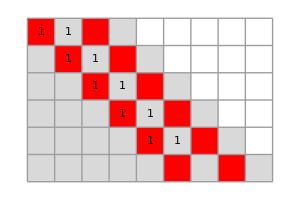

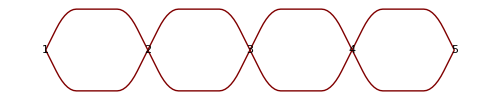
-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
SSSDisplay[SSSSize->300,NetSize->500]
```

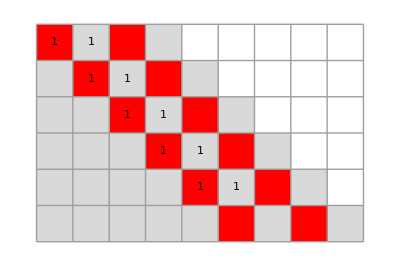
-Graphics- | → | -Graphics-Substitution Rule: -Graphics-

```mathematica
SSSDisplay[ShowRule->Left,NetMethod->None,ImageSize->{Automatic,100},SSSSize->{Automatic,70}]
```

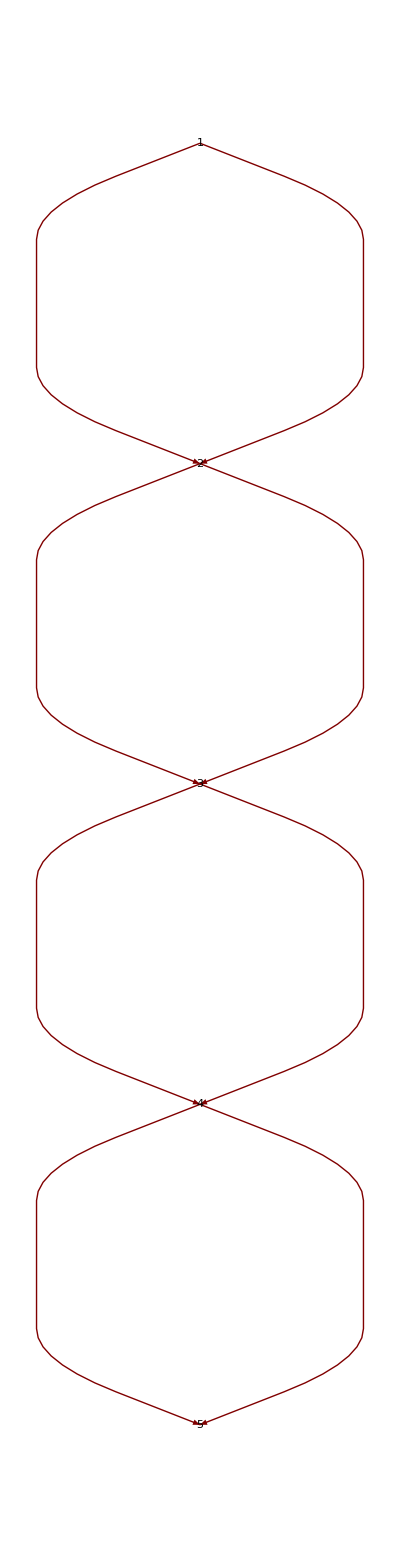
-Graphics- | → | -Graphics-Substitution Rule: -Graphics--Graphics-

```mathematica
SSSDisplay[ShowRule->Left,NetMethod->TreePlot,SSSSize->{Automatic,200},NetSize->{Automatic,300}]
```

```mathematica
SSSDisplay[ShowRule->Left,NetMethod->{},SSSSize->{Automatic,300},ImageSize->{Automatic,300}]
```

-Graphics- | → | -Graphics-Substitution Rule: -Graphics-

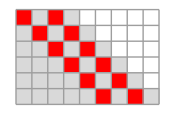
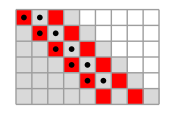
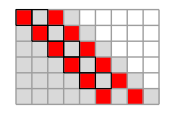
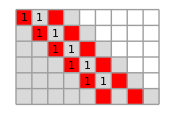
-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

```mathematica
Row[SSSDisplay[HighlightMethod->#,NetMethod->None,ImageSize->175,SSSSize->175]& /@ {None,Dot,Frame,Number}]
```

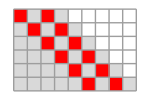
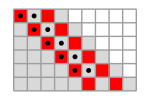
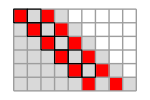
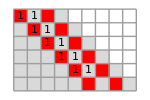
-Graphics- | → | -Graphics-Substitution Rule:-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Flatten@{
SSSRuleIcon[$SSSRules,ImageSize->{Automatic,15}],
SSSDisplay[HighlightMethod->#,ShowRule->None,NetMethod->None,ImageSize->150,SSSSize->150]& 
/@ {None,Dot,Frame,Number}}]
```

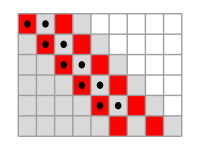
-Graphics- | → | -Graphics-Substitution Rule:
 
-Graphics--Graphics-

```mathematica
SSSDisplay[HighlightMethod->Dot,ShowRule->Top,SSSSize->{200,150},ImageSize->{200,200},NetMethod->GraphPlot,NetSize->500]
```

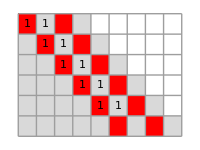
-Graphics- | → | -Graphics-Substitution Rule:
 
-Graphics--Graphics-

```mathematica
SSSDisplay[HighlightMethod->Number,ShowRule->Top,SSSSize->{200,150},ImageSize->{200,200},NetMethod->GraphPlot,NetSize->500]
```

#### SSS

The default workhorse function to build and display SSSs and their causal networks.  (After use, they can be used and redisplayed without rebuilding, using SSSDisplay, etc.)

```mathematica
SSS[rule_,init_,n_Integer,opts___] := (SSSInitialize[init,Quiet]; SSSEvolve[rule,n]; SSSMakeNet; SSSDisplay[opts])
```

```mathematica
SSS::usage="creates and displays a sequential substitution system (SSS) and its causal network. (After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRules, $SSSEvolution and $SSSNet.)";
```

```mathematica
SSS::usage="SSS[rule(s), init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using rule(s) starting with the state init (using string notation), allowing the SSS to evolve for n steps.  
Any options given are passed on to SSSDisplay.

(After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRules, $SSSEvolution and $SSSNet.)";
```

```mathematica
?SSS
```

SSS[
StyleBox["rule",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["init",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["n",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["opts",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]creates and displays a sequential substitution system (SSS) and its causal network, using 
StyleBox["rule",
FontSlant->"Italic"]
StyleBox["(",
FontSlant->"Italic"]
StyleBox["s",
FontSlant->"Italic"]
StyleBox[")",
FontSlant->"Italic"] starting with the state 
StyleBox["init",
FontSlant->"Italic"] (using string notation), allowing the SSS to evolve for 
StyleBox["n",
FontSlant->"Italic"] steps.  
Any options given are passed on to SSSDisplay.

(After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRules, $SSSEvolution and $SSSNet.)

#### SSSAnimate

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
SSSAnimate := Module[{v},
Manipulate[
v=Sort@Thread[VertexList[ $SSSNet]->(VertexCoordinateRules /. Cases[graphtype[$SSSNet], _Rule, Infinity])];
SSSDisplay[HighlightMethod->highlight,ShowRule->Top, ImageSize->{250,485},SSSSize->{200,465},NetSize->{600,485},Max->n,NetMethod->graphtype,VertexLabeling->vertexlabels,VertexCoordinateRules->v⟦;;n-1⟧,
Method->
Switch[graphtype,TreePlot,Automatic,LayeredGraphPlot,Automatic,_,"SpringElectricalEmbedding"]],
{n,3,Length[$SSSEvolution],1,Appearance->"Labeled"},{highlight,{Number,Dot,Frame,None}},{graphtype,{GraphPlot,LayeredGraphPlot,TreePlot,GraphPlot3D}},{vertexlabels,{True,False,Tooltip,All,Automatic}} ] ];
```

```mathematica
SSSAnimate::usage="SSSAnimate produces a manipulatable display of the current SSS (sequential substitution system) and its causal network, allowing the user to see the system evolve step by step and giving easy access to various display parameters.

(This function calls SSSDisplay and uses the information in global variables $SSSRules, $SSSEvolution and $SSSNet.)";
```

```mathematica
?SSSAnimate
```

SSSAnimate produces a manipulatable display of the current SSS (sequential substitution system) and its causal network, allowing the user to see the system evolve step by step and giving easy access to various display parameters.

(This function calls SSSDisplay and uses the information in global variables $SSSRules, $SSSEvolution and $SSSNet.)

#### SSSPut/Get

```mathematica
SSSPut[fname_:"SSS"]:=({$SSSRules,$SSSEvolution,$SSSNet}>>Evaluate@DateString[{"SSS.","Year",".","Month",".","DayShort",".","Hour24Short",".","Minute",".","SecondExact",".txt"}])
```

```mathematica
SSSGet[fname_:""] := If[StringLength[fname]==0,FileNames[]//Column,{$SSSRules,$SSSEvolution,$SSSNet}=Get[fname]]
```

```mathematica
SSSPut::usage="SSSPut[filename] saves the current SSS and causal network to filename, first appending the current date and time information to produce a unique file name.";
```

```mathematica
SSSGet::usage="SSSGet[filename] gets a SSS and causal network from filename.

SSSGet[] calls FileNames to print the list of files in the current directory.  (Use SetDirectory to change directories.)";
```

```mathematica
?SSSPut
```

SSSPut[
StyleBox["filename",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["saves",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["the",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["current",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["SSS",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["and",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["causal",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["network",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["to",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["filename",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["first",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["appending",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["the",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["current",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["date",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["and",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["time",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["information",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["to",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["produce",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["a",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["unique",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["file",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["name",
FontSlant->"Plain"].

```mathematica
?SSSGet
```

SSSGet[
StyleBox["filename",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["gets",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["a",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["SSS",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["and",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["causal",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["network",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["from",
FontSlant->"Plain"]
StyleBox[" ",
FontSlant->"Plain"]
StyleBox["filename",
FontSlant->"Italic"].

SSSGet[] calls FileNames to print the list of files in the current directory.  (Use SetDirectory to change directories.)

```mathematica
(* SSSPut[] *)
```

```mathematica
(* SSSGet[] *)
```

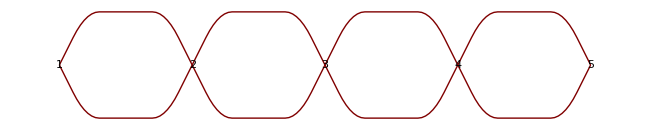
-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
SSSDisplay[NetSize->{650,Automatic}]
```

```mathematica
Directory[]
```

```mathematica
(* SetDirectory["I:\\Caviness\\Research"] *)
```

```mathematica
SetDirectory["C:\\Users\\caviness\\Documents\\Work\\Research\\SSSCausalNetworks"]
```

```mathematica
FileNames[]
```

### Loop through all rulesets

#### Universal Enumeration of RuleSets

```mathematica
characterWeights = Prepend[Thread[CharacterRange["A","Z"]->Range[26]],""->0];
```

```mathematica
UnrankRuleSet[iplusflag_Integer/;iplusflag>0] := Module[{i,extraflag,n,j,quaternaryDigits,numberOfEOS,chopPos,extra,maxDigit,ans={{1}},strings,ruleset},
extraflag = OddQ[iplusflag];
i=Quotient[iplusflag+1,2];       (* offset so i can start at 1 *)
n=Floor[Log[4,3 i-2]];
j=i-(4^n+2)/3;
quaternaryDigits=IntegerDigits[j,4,n];
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{1}}] ,
1,AppendTo[ans,{1}],
2,AppendTo[ans⟦-1⟧,1],
3,ans⟦-1⟧⟦-1⟧++
]&,
quaternaryDigits];
maxDigit=Max[Flatten@ans];
strings=StringJoin @@@ (ans  /. (Reverse /@ characterWeights⟦;;maxDigit+1⟧));
If[extraflag,strings=Join[Most[strings],{"",Last[strings]}]];
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
Rule @@@ Partition[strings,2,2]
];
```

```mathematica
RankRuleSet[rs_List] := Module[{rl,wl,w,code="",extrabit=1},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
If[Length[rl]>1 && rl⟦-2⟧=="",extrabit=0;rl=Drop[rl,{-2}]]; 
(* remove "→" and drop penultimate empty string, if needed *)
wl=(Characters/@ rl) //. characterWeights; (* to lists of lists of numbers "A"->1, etc. *)
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}},
If[wl⟦-1⟧⟦-1⟧>1, code="3"<>code; wl⟦-1⟧⟦-1⟧--,
If[wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  code="2"<>code; wl⟦-1⟧=Most[wl⟦-1⟧],
If[Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, code="0"<>code; wl=Drop[wl,-2],
If[wl⟦-1⟧=={1},  code="1"<>code; wl=Drop[wl,-1]]]]]];
2(FromDigits[code,4]+(4^(w-1)+2)/3)+extrabit-1](* add number of rulesets of smaller weights to reconstructed quaternary code, leftshift and add extrabit at the end, subtract 1 so we can start at 1 instead of at 2 (2 × basic ruleset number, which has a minimum of 1) *)
```

```mathematica
Clear[UniqueRuleSetQ];
UniqueRuleSetQ[n_Integer] := 
Module[{rs,lhs,max,i,j,dup,strings,distinctChars},
rs=UnrankRuleSet[n];
If[RankRuleSet[rs]≠n,dup=True,            (* returns a different index *)
strings=Flatten[List @@@ rs];
distinctChars=Union[Flatten[Characters /@ strings]];
If[characterWeights⟦2;;,1⟧⟦Length[#]⟧≠Last[#]& @ distinctChars,dup=True, (* skips characters, renaming possible *)
If[(Length[rs]==1),dup=False,           (* only 1 rule, must be unique *)
lhs=First /@ rs;
max=Length[lhs];
i=1;j=2;dup=False;
While[!dup && i<max,
If[Length[StringPosition[lhs⟦j⟧,lhs⟦i⟧]]>0,dup=True];
j++;
If[j>max,i++; j=i+1]]]]];
!dup]
```

```mathematica
NonSoloIdentityRulePosition[rs_List] := Module[{eqPos},
eqPos=Flatten@Position[(Equal@@@rs),True,1,1];
If[eqPos=={} || Length[rs]==1,0,First@eqPos]]
```

```mathematica
ConflictingRulesPosition[rs_List] := Module[{lhs,max,i,j,found},
lhs=First /@ rs;
max=Length[lhs];
i=1;j=2;found=False;
While[!found && i<max,
If[Length[StringPosition[lhs⟦j⟧,lhs⟦i⟧]]>0,found=True;Return[{i,j}]];
j++;
If[j>max,i++; j=i+1]];
{}];
```

```mathematica
RateRuleSet[n_Integer] := 
Module[{rs,lhs,max,i,j,response,strings,distinctChars,nsirp,crp},
rs=UnrankRuleSet[n];
Which[
(*1*) RankRuleSet[rs]≠n,response="duplicate",            (* returns a different index *)

strings=Flatten[List @@@ rs];
distinctChars=Union[Flatten[Characters /@ strings]];

(*2*) characterWeights⟦2;;,1⟧⟦Length[#]⟧≠Last[#]& @ distinctChars,response="renamed duplicate: reduces to simpler ruleset after renaming", (* skips characters, renaming possible *)

(*3*) (Length[rs]==1),response="ok",           (* only 1 rule, must be unique *)

(*4*) (nsirp=NonSoloIdentityRulePosition[rs])>0, response = "non-solo identity rule: "<>ToString[nsirp],

(*5*) Length[crp=ConflictingRulesPosition[rs]]>0, response="rule "<>ToString[crp⟦1⟧]<>" conflicts with rule "<>ToString[crp⟦2⟧],

True,response="ok"
];
response]
```

#### RuleSet length & weight, string weight

```mathematica
RuleSetLength[rs_List] := StringLength[StringJoin @@ (StringJoin @@@ rs)]
```

```mathematica
RuleSetWeight[rs_List] :=Plus@@(Characters[StringJoin @@ (StringJoin @@@ rs)]//.characterWeights)
```

```mathematica
StringWeight[s_String] :=Plus@@(Characters[s]//.characterWeights)
```

#### Initial string for a given ruleset

```mathematica
Clear[nextLyndon,deBruijn];
nextLyndon[k_,n_,w_List] := Module[{x=Table[0,{n}],l=Length[w],lastchar=n},
x=w⟦Mod[Range[1,n],l,1]⟧;   (* permute the digits appropriately *)
While[lastchar≥0 && x⟦lastchar⟧==k-1,lastchar--];  (* back up past end trash *)
If[lastchar==0,
{}, (* nothing left, we're done *)
x⟦lastchar⟧++;x⟦;;lastchar⟧  (* increment last digit, return appropriate part *)
]];
deBruijn[k_,n_] := deBruijn[k,n]=Module[{s,d=Divisors[n]},
s=NestWhileList[nextLyndon[k,n,#]&,{0},#≠{}&];
Join @@ Select[s,MemberQ[d,Length[#]]&]
];
```

```mathematica
SSSInitialState[rs_List] := Module[{s,k,n,chars,strings,len},
strings=Union[First /@ rs];
If[strings=={}||strings=={""},strings={"A"}];
chars=Union[Flatten[Characters /@  strings]];
k=Length[chars];
n=Max[StringLength/@strings];
s=deBruijn[k,n]⟦Mod[Range[k^n+n-1],k^n,1]⟧;
(* Print[strings,chars,k,n,s]; *)
StringJoin[s /. Thread[Range[k]-1->chars]]
]
```

```mathematica
UnrankRuleSet /@ Select[Range[100],RateRuleSet[#]==="ok"&]
```

{{→A},{A→},{A→,→A},{A→A},{→AA},{AA→},{A→,→AA},{A→,→B},{A→AA},{A→,B→},{A→B},{AA→,→A},{AA→,A→},{AA→A},{→AAA},{AAA→},{→AB},{AB→},{B→,→A},{B→,A→},{B→A},{→BA},{BA→},{A→,→AAA},{A→,→AB},{A→,B→,→A},{A→,B→A},{A→,→BA},{A→AA,→A},{A→AAA},{A→AB}}

```mathematica
{#,SSSInitialState[#]}&/@%//Grid
```

{→A} | A
{A→} | A
{A→,→A} | A
{A→A} | A
{→AA} | A
{AA→} | AA
{A→,→AA} | A
{A→,→B} | A
{A→AA} | A
{A→,B→} | AB
{A→B} | A
{AA→,→A} | AA
{AA→,A→} | AA
{AA→A} | AA
{→AAA} | A
{AAA→} | AAA
{→AB} | A
{AB→} | AABBA
{B→,→A} | B
{B→,A→} | AB
{B→A} | B
{→BA} | A
{BA→} | AABBA
{A→,→AAA} | A
{A→,→AB} | A
{A→,B→,→A} | AB
{A→,B→A} | AB
{A→,→BA} | A
{A→AA,→A} | A
{A→AAA} | A
{A→AB} | A

```mathematica
characterWeights⟦2;;,1⟧
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

#### Identify the SSS: SSSLastChange, SSSRepetitionInterval, SSSRepetitionStart

For SSSLastChange, use $SSSEvolution as is, to guarantee that the lines considered equal are not duplicates created by "A"→"A" rules.  (It's not a duplicate if there are cells replaced by same color cells, only if the cells are identical and unchanged.)

```mathematica
SSSLastChange := Module[{last,n},
last=Last[$SSSEvolution];
n=Length[$SSSEvolution];
While[(n>1) && ($SSSEvolution⟦n⟧==last), n--];
n+1]
```

Use the stripped version of $SSSEvolution when looking for repetitions:

```mathematica
SSSRepetitionInterval := Module[{evol=SSSStrip /@ $SSSEvolution},
If[Length@#>1,#⟦-1⟧-#⟦-2⟧,0]&@Flatten@Position[evol,Last@evol]]
```

```mathematica
Length[$SSSEvolution]
```

21

```mathematica
SSSStrip/@$SSSEvolution
```

{CABD,CBAAABD,CBAABAAABD,CBABAAABAAABD,CBBAAABAAABAAABD,CBBAABAAABAAABAAABD,CBBABAAABAAABAAABAAABD,CBBBAAABAAABAAABAAABAAABD,CBBBAABAAABAAABAAABAAABAAABD,CBBBABAAABAAABAAABAAABAAABAAABD,CBBBBAAABAAABAAABAAABAAABAAABAAABD,CBBBBAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBABAAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBBAAABAAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBBAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBBABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBBBAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBBBAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBBBABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBBBBAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD,CBBBBBBBAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD}

```mathematica
stringPrePost[{s_String,{n_,m_}}] := StringTake[s,#]& /@ { {1,n-1}, {m+1,-1} }  (* return parts of string before n and after m, {} if appropriate *)
```

```mathematica
SSSEffectiveRepetitionInterval := Module[{ev=$SSSEvolution,evStripped,cellMatch,rulesApplied},
(* Note: here, unlike in the similar code in SSSDisplay, numerical order = top-down.  There, Reverse set up for ArrayPrint *)
(* The following line first takes pairs of lines from ev and hands them to cellsDeleted which return the positions (if any) of cells that were deleted in the first of the pair.  Finally return a pair of indices giving the first and last position of the match (or {1,0} for no match), which stringPrePost uses to find the parts of each string in evStripped before/after match *)
cellMatch=If[Length[#]==0,{1,0} (* nothing deleted *),{First[#],Last[#]}]& /@ cellsDeleted /@ Partition[ev,2,1];
evStripped=Most[SSSStrip /@ ev];
rulesApplied=MapIndexed[SSSStrip@ev[[First@#2,#1]]&,cellsDeleted /@ Partition[ev,2,1]] /. MapIndexed[First@#1->First@#2&,Flatten[{$SSSRules}]];
Print@cellMatch;
stringPrePost /@ Transpose[{evStripped,cellMatch}] //Print;
Print[Column[First/@cellMatch]," ",Column[stringPrePost /@ Transpose[{evStripped,cellMatch}]],"  ",Column@rulesApplied];
];
SSSEffectiveRepetitionInterval
```

{{2,3},{5,6},{4,5},{3,4},{6,7},{5,6},{4,5},{7,8},{6,7},{5,6},{8,9},{7,8},{6,7},{9,10},{8,9},{7,8},{10,11},{9,10},{8,9},{11,12}}

{{C,D},{CBAA,D},{CBA,AAABD},{CB,AAABAAABD},{CBBAA,AAABAAABD},{CBBA,AAABAAABAAABD},{CBB,AAABAAABAAABAAABD},{CBBBAA,AAABAAABAAABAAABD},{CBBBA,AAABAAABAAABAAABAAABD},{CBBB,AAABAAABAAABAAABAAABAAABD},{CBBBBAA,AAABAAABAAABAAABAAABAAABD},{CBBBBA,AAABAAABAAABAAABAAABAAABAAABD},{CBBBB,AAABAAABAAABAAABAAABAAABAAABAAABD},{CBBBBBAA,AAABAAABAAABAAABAAABAAABAAABAAABD},{CBBBBBA,AAABAAABAAABAAABAAABAAABAAABAAABAAABD},{CBBBBB,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD},{CBBBBBBAA,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD},{CBBBBBBA,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD},{CBBBBBB,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD},{CBBBBBBBAA,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD}}

2
5
4
3
6
5
4
7
6
5
8
7
6
9
8
7
10
9
8
11 {C,D}
{CBAA,D}
{CBA,AAABD}
{CB,AAABAAABD}
{CBBAA,AAABAAABD}
{CBBA,AAABAAABAAABD}
{CBB,AAABAAABAAABAAABD}
{CBBBAA,AAABAAABAAABAAABD}
{CBBBA,AAABAAABAAABAAABAAABD}
{CBBB,AAABAAABAAABAAABAAABAAABD}
{CBBBBAA,AAABAAABAAABAAABAAABAAABD}
{CBBBBA,AAABAAABAAABAAABAAABAAABAAABD}
{CBBBB,AAABAAABAAABAAABAAABAAABAAABAAABD}
{CBBBBBAA,AAABAAABAAABAAABAAABAAABAAABAAABD}
{CBBBBBA,AAABAAABAAABAAABAAABAAABAAABAAABAAABD}
{CBBBBB,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD}
{CBBBBBBAA,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD}
{CBBBBBBA,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD}
{CBBBBBB,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD}
{CBBBBBBBAA,AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD}  1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1

```mathematica
First/@{{2,3},{5,6},{4,5},{3,4},{6,7},{5,6},{4,5},{7,8},{6,7},{5,6},{8,9},{7,8},{6,7},{9,10},{8,9},{7,8},{10,11},{9,10},{8,9},{11,12}}
```

{2,5,4,3,6,5,4,7,6,5,8,7,6,9,8,7,10,9,8,11}

```mathematica
Differences[{2,5,4,3,6,5,4,7,6,5,8,7,6,9,8,7,10,9,8,11},1]
```

{3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3}

```mathematica
tryOffset[l_List,n_Integer]:= l[[n+1;;]]-l[[;;-n-1]]
```

```mathematica
tryOffset[{2,5,4,3,6,5,4,7,6,5,8,7,6,9,8,7,10,9,8,11},#]& /@ Range[11]//Column
```

{3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3}
{2,-2,2,2,-2,2,2,-2,2,2,-2,2,2,-2,2,2,-2,2}
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
{4,0,0,4,0,0,4,0,0,4,0,0,4,0,0,4}
{3,-1,3,3,-1,3,3,-1,3,3,-1,3,3,-1,3}
{2,2,2,2,2,2,2,2,2,2,2,2,2,2}
{5,1,1,5,1,1,5,1,1,5,1,1,5}
{4,0,4,4,0,4,4,0,4,4,0,4}
{3,3,3,3,3,3,3,3,3,3,3}
{6,2,2,6,2,2,6,2,2,6}
{5,1,5,5,1,5,5,1,5}

```mathematica
tryOffset[{2,5,4,3,6,5,4,7,6,5,8,7,6,9,8,7,10,9,8,11},#]& /@ Range[11]
```

```mathematica
Differences
```

```mathematica
pos= {{2,3},{5,6},{4,5},{3,4},{6,7},{5,6},{4,5},{7,8},{6,7},{5,6},{8,9},{7,8},{6,7},{9,10},{8,9},{7,8},{10,11},{9,10},{8,9},{11,12}};
```

{{2,3},{5,6},{4,5},{3,4},{6,7},{5,6},{4,5},{7,8},{6,7},{5,6},{8,9},{7,8},{6,7},{9,10},{8,9},{7,8},{10,11},{9,10},{8,9},{11,12}}

```mathematica
Last /@ pos
```

{3,6,5,4,7,6,5,8,7,6,9,8,7,10,9,8,11,10,9,12}

```mathematica
ListPlot[Last /@ pos]
```

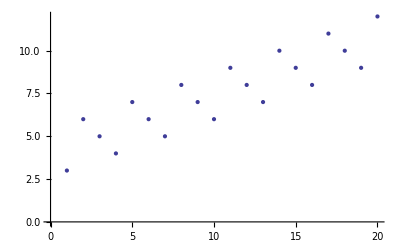

```mathematica
First /@ pos
```

{2,5,4,3,6,5,4,7,6,5,8,7,6,9,8,7,10,9,8,11}

```mathematica
a=Differences[{2,5,4,2,5,4,2,5,4,2,5,4,2,5,4,2,5,4,2,5,4},1]
```

{3,-1,-2,3,-1,-2,3,-1,-2,3,-1,-2,3,-1,-2,3,-1,-2,3,-1}

```mathematica
a/.{x___,q:Longest[Repeated[p__,{2,∞}]]}:>{q}
```

{-2,3,-1,-2,3,-1,-2,3,-1,-2,3,-1,-2,3,-1,-2,3,-1}

```mathematica
%/.{q:Repeated[p__,{2,∞}]}:>{Length[{p}],Total[{p}]}
```

{3,0}

```mathematica
a=Differences[First /@ pos,1]
```

{3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3}

```mathematica
a/.{x___,q:Longest[Repeated[p__,{2,∞}]]}:>{q}
```

{-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3,-1,-1,3}

```mathematica
%/.{q:Repeated[p__,{2,∞}]}:>{Length[{p}],Total[{p}]}
```

{3,1}

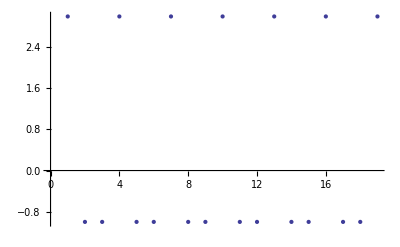

```mathematica
ListPlot[Differences[First /@ pos]]
```

```mathematica
Rest[FoldList[Plus,2,Differences[First /@ pos]]]
```

{5,4,3,6,5,4,7,6,5,8,7,6,9,8,7,10,9,8,11}

```mathematica
% /.{x___,q:Longest[Repeated[p__,{2,∞}]]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{3},{-1, -1, 3, -1, -1, 3, -1, -1, 3}×2}

```mathematica
1/0.3473684210526315
```

2.87879

```mathematica
SequenceAlignment["CBBBBA","CBBBBBBBAA"]
```

{CBBBB,{,BBBA},A}

```mathematica
{}/.{x___,q:Longest[Repeated[p__,{2,∞}]],y___}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]],{y}}
```

{}

```mathematica
Characters@"CBBBBBBBAA"
```

{C,B,B,B,B,B,B,B,A,A}

```mathematica
Characters@"CBBBBBBBAA"/.{x___,q:Longest[Repeated[p__,{2,∞}]],y___}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]],{y}}
```

{{C},{B}×7,{A,A}}

```mathematica
Characters@"AAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABAAABD"/.{x___,q:Longest[Repeated[p__,{2,∞}]],y___}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]],{y}}
```

```mathematica
(Characters@"AAABAAABAAABAAABAAABAAABD")/.{Shortest[x___],q:Repeated[p__,{2,∞}],Shortest[y___]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]],{y}}
```

{{},{A, A, A, B}×6,{D}}

```mathematica
(Characters@"AAABAAABAAABAAABAAABAAABD")/.{x___,q:Repeated[Longest[p__],{2,∞}],y___}:>{{x},{q},{y}} // Timing
```

{8.471,{{},{A,A,A,B,A,A,A,B,A,A,A,B,A,A,A,B,A,A,A,B,A,A,A,B},{D}}}

```mathematica
(Characters@"AAABAAABAAABAAABAAABAAABD")/.{x___,q:Longest[Repeated[p__,{2,∞}]],y___}:>{{x},{q},{y}} // Timing
```

{8.44,{{},{A,A,A,B,A,A,A,B,A,A,A,B,A,A,A,B,A,A,A,B,A,A,A,B},{D}}}

```mathematica
{"A","A","A","B","A","A","A","B","A","A","A","B","A","A","A","B","A","A","A","B","A","A","A","B"}/.{q:Repeated[p__,{2,∞}]}:>{ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}//Timing
```

{4.29,{{A, A, A, B}×6}}

```mathematica
Characters@"AAABAAABAAABAAABD"/.{q:Longest[Repeated[p__,{2,∞}]],y___}:>{ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]],{y}}
```

{{A, A, A, B, A, A, A, B}×2,{D}}

```mathematica
Characters["AAAAAAAAAAAAAAAAAAAC"]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,C}

```mathematica
Characters["CAAAAAAAAAAAAAAAAAAA"]/.{x___,q:Longest[Repeated[p__,{2,∞}]]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{C},{A}×19}

```mathematica
Characters["AABAABAABAABAABAABAABAABAABC"]
```

```mathematica
Characters["CAABAABAABAABAAB"]/.{x___,q:Longest[Repeated[p__,{2,∞}]]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{C},{A, A, B}×5}

```mathematica
Characters["CAABAABAABAABAABAABAAB"]/.{x___,q:Longest[Repeated[p__,{2,∞}]]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{C},{A, A, B}×7}

```mathematica
Characters["CAAAAAAAAAAAAAAAAAAA"]/.{x___,q:Longest[Repeated[p__,{2,∞}]]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{C},{A}×19}

```mathematica
{0,1,2,3,0,0,1,0,1,0,1}/.{x___,q:Longest[Repeated[p__,{2,∞}]]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{0,1,2,3,0},{0, 1}×3}

```mathematica
{0,1,2,3,0,0,0,1,0,1,0,1,0,1}/.{x___,q:Repeated[p__,{2,∞}]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{0,1,2,3,0,0},{0, 1}×4}

```mathematica
{0,1,2,3,0,0,0,1,0,1,0,1,0,1,0,1}/.{x___,q:Repeated[p__,{2,∞}]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{0,1,2,3,0,0},{0, 1}×5}

```mathematica
{0,1,2,3,0,0,0,1,0,1,0,1,0,1,0,1,0,1}/.{x___,q:Repeated[p__,{2,∞}]}:>{{x},ToString[{p}]<>"×"<>ToString[Length[{q}]/Length[{p}]]}
```

{{0,1,2,3,0,0},{0, 1}×6}

Use as adjusted initial state the first shortest-length, least-weight string from among the current (stripped) lines of $SSSEvolution:

```mathematica
SSSRepetitionStart := Module[{evol=SSSStrip /@ $SSSEvolution,i,j,stillrepeating=True,sssRI},
sssRI=SSSRepetitionInterval;
(*  Print@sssRI; *)
If[sssRI==0,Return[0]];          (* no SSS repetition *)
j=Length[evol]-sssRI;
(* Print@j; *)
While[stillrepeating && (j≥1),
If[evol⟦j⟧==evol⟦j+sssRI⟧,j -= sssRI,stillrepeating=False]];
j+=sssRI;
stillrepeating=True;
While[stillrepeating && (j≥1),
If[evol⟦j⟧==evol⟦j+sssRI⟧,j--,stillrepeating=False]];
j+1  (* returns index to _SSS_ starting location! *)
]
```

```mathematica
SSSAdjustedInitialState:= Module[{evol=SSSStrip /@ $SSSEvolution,sssRI,reduced,minLength,minWeight},
If[(sssRI=SSSRepetitionStart)>0,evol=evol⟦sssRI;;⟧];
minLength=Min[StringLength/@evol];
reduced=Select[evol,StringLength[#]==minLength &];
minWeight=Min[StringWeight/@reduced];
First[Select[reduced,StringWeight[#]==minWeight&]]
]
```

#### Identify the network: SSSColors, SSSNetFilter, SSSReindex, SSSNetRepetitionInterval, SSSNetRepetitionStart, BestNetStart

Return a string containing each character that appears anywhere in $SSSEvolution:

```mathematica
SSSColors:= StringJoin@Union@Flatten@Characters[SSSStrip /@ $SSSEvolution]
```

Return a subset of net/graph containing edges with initial vertex between start and stop (no limits on ending vertex of the edges):

```mathematica
SSSNetFilter[net_List,start_Integer,stop_Integer] := DeleteCases[net,Rule[_?(#<start||#>stop&),_]]
```

Reindex a net (graph) so that the smallest index listed is always 1:

```mathematica
SSSReindex[net_List] := Module[{min=Min[List@@@net]},If[min==1, net, Map[#-min+1&, net, {2}]]]
```

Assuming $SSSNet has length 500, skip the first 100 edges, then compare the next 200 edges to a shifting set of 200, letting the offset start at 1 and increase until a match is found (or give up after 200 edges).  This gives the net repetion interval.

```mathematica
SSSNetRepetitionInterval:=Module[{origSlice,netRepeatInterval,j},
If[SSSLastChange < Length[$SSSEvolution],Return[0]];
origSlice=Map[-100+1+#& ,SSSNetFilter[$SSSNet,100,300],{2}];
j=1;
netRepeatInterval=0;
While[j≤200 && netRepeatInterval==0,
If[origSlice===Map[-100-j+1+#& ,SSSNetFilter[$SSSNet,100+j,300+j],{2}],
netRepeatInterval=j];
j++];
netRepeatInterval
]
```

Find the start of the net repetition:

```mathematica
SSSNetRepetitionStart := Module[{slice1,slice2,j,stillrepeating=True,sssNRI},
sssNRI=SSSNetRepetitionInterval;
(*  Print@sssNRI; *)
If[sssNRI==0,Return[0]];          (* no net repetition *)
j=500+1-3 sssNRI;
(* Print@j; *)
While[stillrepeating && (j≥1),
(* Print[j,", ",sssNRI+j-1,", ",sssNRI+j,", ",2sssNRI+j-1,": ",Sort[SSSReindex[SSSNetFilter[$SSSNet,j,sssNRI+j-1]]]===Sort[SSSReindex[SSSNetFilter[$SSSNet,sssNRI+j,2sssNRI+j-1]]]]; *)
If[Sort[SSSReindex[SSSNetFilter[$SSSNet,j,sssNRI+j-1]]]===Sort[SSSReindex[SSSNetFilter[$SSSNet,sssNRI+j,2sssNRI+j-1]]],j--,stillrepeating=False]];
(* Print[j+1]; *)
j+1  (* returns index to _SSS_ starting location! *)
]
```

Find best network starting position:  Find OutDegree-InDegree for each vertex, look for first largest (positive) jump in these values:  this looks for a place where there was low (relative) outdegree followed by high (relative) outdegree.

```mathematica
BestNetStart[net_List] := Module[{mx=Max[List@@@net]},
1+(First@First[Position[#,Max[#]]])&@
Differences[(Length @ Cases[$SSSNet,Rule[#,_]->#]& /@ Range[1,mx])-(Length @ Cases[$SSSNet,Rule[_,#]->#]& /@ Range[1,mx])]] (* returns _net_ starting location! *)
```

#### Ruleset Tests: Conditions for skipping the ruleset immediately

1. "duplicate": Duplicate ruleset.  1/4 of the indices return duplicates.  Test by checking whether UnrankRuleSet returns the original index.
2. "renamed duplicate": Any ruleset that omits characters can be renamed as a simpler one.
3. "non-solo identity": Ruleset contains an identity rule, such as A→A, in a non-final position.
4. "conflicts":  A rule's left hand side is a substring of a later rule's left hand side -- the second one cannot ever be invoked.  This ruleset is functionally equivalent to the simpler one obtained by deleting the unused rule.

In the last two cases, we will try to jump past all rulesets sharing this problem.

Note on identity rules:  
If an identity rule is followed by one or more other rules, they will never be executed if the identity rule matches so the ruleset is functionally equivalent to the one without those other rules, or if the identity rule never matches the ruleset is functionally equivalent to the one with the identity rule omitted:  so in either case, a ruleset with a non-final identity rule can be skipped.  Depending on the initial state, the behavior switches between behaviors of two simpler rulesets.
If an identity rule in final position is preceded by one or more other rules, it may or may not be executed: if not, the behavior matches that of the simpler ruleset from which the identity rule has been removed; on the other hand if the identity rule is ever executed, it will be used exclusively thereafter, mimicking the behavior of the ruleset containing the identity rule alone.  So in either case, a ruleset with a final identity rule and other rules can be skipped.  Depending on the initial state, the behavior switches between behaviors of two simpler rulesets.
To summarize: rulesets with non-solo identity rules can be skipped.

#### Musings on long jumps

Hmmm.  Actually, I could have the computer search for long uninterrupted sequences of the two “identity” & “conflict” messages.  The point is, in these cases maybe it’s possible to jump ahead a long ways in the list of rulesets.  I have the glimmerings of an idea.  Maybe writing it down will help it jell:

First, an example:  All of these would be skipped because of the non-final identity rule in the second position:

33579 :  {AB→,A→A,→A,→A,→,A→} ,  non-final identity rule
...
33642 :  {AB→,A→A,C→} ,  non-final identity rule

None of the stuff that comes after rule 2 matters at all.  The mere fact that there IS something after means that the identity rule is non-final, and all of these cases are skipped.  I notice some “duplicate” messages, but I guess that doesn’t matter after all, those would be skipped by the non-final identity rule test.  Now the stuff after rule 2 has collective weight 3, and progresses from many rules, many null strings and single A’s up through cases with fewer rules, longer strings, and finally ends with 1 rule with one string of 1 largest-possible character.  For weight 3, that means a single C.  So rather than iterating through all these cases, I should notice the non-final identity situation, find the weight of the stuff that follows, jump to the last of the run of cases that will be dropped because of the same situation, here that means replacing the “stuff that follows” by C→ , in other words, replace {AB→,A→A,→A,→A,→,A→} by {AB→,A→A,C→} and convert it back to an index (here, 33642) and then continue on through the list.

Yes, I think that will work, and it will make the program run much faster.  Ok, what about cases with the “conflict” message?  Here’s run of them:

32939 :  {AAB→,A→,A→,A→,→A} ,  rule 2 conflicts with rule 3
...
32954 :  {AAB→,A→,A→B} ,  rule 2 conflicts with rule 3

32955 :  {AAB→,A→,AA→,→A} ,  rule 2 conflicts with rule 3
32956 :  {AAB→,A→,AA→,A→} ,  duplicate
32957 :  {AAB→,A→,AA→,A→} ,  rule 2 conflicts with rule 3
32958 :  {AAB→,A→,AA→A} ,  rule 2 conflicts with rule 3
32959 :  {AAB→,A→,→AAA} , Some symbols die out, SSS reduces to simpler case
32960 :  {AAB→,A→,AAA→} ,  duplicate
32961 :  {AAB→,A→,→AB} ,  78  networks like  65
32962 :  {AAB→,A→,AB→} ,  duplicate
32963 :  {AAB→,A→,B→,→A} , Some symbols die out, SSS reduces to simpler case
32964 :  {AAB→,A→,B→,A→} ,  duplicate
32965 :  {AAB→,A→,B→,A→} ,  rule 2 conflicts with rule 4
32966 :  {AAB→,A→,B→A} , SSS died at step  13
32967 :  {AAB→,A→,→BA} ,  79  networks like  65
32968 :  {AAB→,A→,BA→} ,  duplicate
32969 :  {AAB→,A→,→C} , no network
32970 :  {AAB→,A→,C→} ,  duplicate
                  
In 32939, it’s the first two A→ rules that conflict.  I could take the weight of whatever follows rule 3 (here that is A→,→A, weight 2) and jump directly to 32946 :  {AAB→,A→,A→,B→}.  But notice that there are still more that will be skipped, maybe it is safe to jump all the way to 32954 :  {AAB→,A→,A→B}.  Not all of the cases in between have two A→rules, but they all have a second rule with a left hand side of A.  Yes, I think that’s probably still safe to do.  But I should to start with have the program list the rulesets to be jumped over for human verification before doing it for real.

I do not think it’s safe to jump farther to rules like {AAB→,A→,AA→A}. Looking farther on in the list the letters jump around and there are even some that would not be skipped by this rule at all, mixed in with those that would:  

32959: {AAB->,A->,->AAA}, Some symbols die out, SSS reduces to simpler case

In this case it’s thrown out for a different reason, but we can’t count on that.  Ok, in case of a “conflict” message, such as {AAB→,A→,A→,A→,→A} ,  rule 2 conflicts with rule 3, I take the weight of the stuff that follows (here A→,→A, weight 2) and jump directly to {AAB→,A→,A→B}, index 32954.  

Similarly, 32955 :  {AAB→,A→,AA→,→A} triggers a “conflict” message, weight following is 1, we jump to 32958 :  {AAB→,A→,AA→A}, don’t save much time but don’t lose anything.  If the “weight following” is 0, don’t try to jump, just go on as usual.  In fact, with the irregularities in the progression of rulesets due to inserted null strings near the end of the ruleset, it might be smart for me to only try to jump if the “weight following” is at least 2.  It’s only the long jumps that save much time, anyway.

#### SSS Tests: Conditions for skipping the ruleset based on features of the SSS

5. Last change in SSS occurs before the final step. Tests using $SSSEvolution, including tags:  in the rule A->A, a cell is destroyed, another is created - even though it looks the same, the tags are different.)  Hypothesis: Identity rules can only produce (singly or multiply linked) chains.  (Tested again after adjusting initial state.)
6. Adjusted SSS does not contain all colors/letters, so this effectively reduces to a duplicate of a simpler ruleset (and net).  (Unadjusted SSS always contains all symbols, by virtue of the default initial state chosen.)

#### Net Tests: Conditions for skipping the ruleset based on features of $SSSNet

7. Empty $SSSNet, no network.  (Tested again after adjusting initial state.)
8. Last change to the net happened before event 100 (while SSS has 500 steps).
9. Already seen an identical network, log it but don't bother displaying it.  (If repeating, log using a concise form.)
10. Net repetion is checked by skipping the first 100, then matching the next 200 edges against 200 edges with a beginning position sliding forward until a match is found or we've used up the 500 events generated.

#### Adjustments

1. Adjusted initial state for SSS: last shortest row (of first 15), repeat until no shorter row is found.  Usually gets past initial junk.
1'. Adjusted initial state for SSS: first least weight row (of first 15), repeat until no lesser weight row is found.  More often gets past initial junk. [Supersedes 1.]
2. If the first vertex of the network is not 1, subtract off a constant from all vertex numbers to make it 1.
2'. If network repeats, find the beginning of the first repetition, note the corresponding row in the SSS and restart using that as the adjusted initial state. [Supersedes 2.]

#### Still problematic

Why does the “duplicate” ruleset seem to always appear before the “non-duplicate” one?  Sigh.  
Try subtracting 1 instead of adding?  FAIL!
Problem is that next-to-last empty string is removed and interpreted as extrabitflag in all cases.  But sometimes it wasn't generated by the extrabitflag, it occurred in the normal progression.

#### SSSTest

```mathematica
Buttoned=True;
```

```mathematica
Clear[SSSTest];
SSSTest[i_,rs_,btn_,vrb_,k_] := Module[{rsr,rsw,rsl,ans,sssIS,sssAIS,sssTempPic,sssRI,lastNetAddition,sssNRS,sssBNS,sssNRI,sssNF,info,displayed=False},
rsr=RateRuleSet[i];
rsw=RuleSetWeight[rs]; 
rsl=RuleSetLength[rs];
sssIS=SSSInitialState[rs];
If[vrb≥10,Print[i,": ",rs, ", sssIS: ",sssIS]];
If[btn≠Buttoned,info={Row@{"weight: ",rsw,", length: ",rsl}}];

Which[
(*1*) rsr≠ "ok",If[vrb≥6,Print[i,": ",rs, ", ",rsr]],

ans={SSS[rs,sssIS,20,NetMethod->{},ShowRule->Top]};

(*2*) $SSSNet==={},If[vrb≥7,Print[i,": ",rs,", no network"]],

(*3*) SSSLastChange<Length[$SSSEvolution], If[vrb≥7,Print[i,": ",rs,", SSS died at step ", SSSLastChange]],

sssAIS=SSSAdjustedInitialState;      (* adjust initial state based on identified SSS repetition *)
If[sssAIS≠sssIS,                                         (* sssAIS defined and kept up-to-date from this point on *)
sssAIS=FixedPoint[Function[{is}, sssTempPic=SSS[rs,is,20,NetMethod->{},ShowRule->Top];If[StringLength[#]<StringLength[is] || (StringLength[#]==StringLength[is] && StringWeight[#]<StringWeight[is]),#,is]&[SSSAdjustedInitialState]], sssAIS];
If[vrb≥2,AppendTo[ans, sssTempPic]];
If[vrb≥10,Print["Adjusted Initial State: ",sssAIS," (took first least weight shortest row)"]];
];

If[vrb≥10,Print["Generating large network"]];

(* look for longer SSS repetition interval if needed *)
If[(sssRI=SSSRepetitionInterval)≠0,         (* sssRI defined and kept up-to-date from this point on *)
SSS[rs,sssAIS,500,NetMethod->{NoSSS}], (* go on, already know it *)
SSS[rs,sssAIS,500,NetMethod->{NoSSS}]; (* check again... *)
If[(sssRI=SSSRepetitionInterval)≠0,
sssAIS=SSSAdjustedInitialState;
If[vrb≥10,Print["Regenerating small network"]];
sssTempPic=SSS[rs,sssAIS,20,NetMethod->{},ShowRule->Top];If[vrb≥2,AppendTo[ans, sssTempPic]];
If[vrb≥10,Print["Regenerating large network"]];
SSS[rs,sssAIS,500,NetMethod->{NoSSS}];
];
];

(*2*) $SSSNet==={},If[vrb≥7,Print[i,": ",rs,", no network"]],

(*3*) SSSLastChange<Length[$SSSEvolution], If[vrb≥7,Print[i,": ",rs,", SSS died at step ", SSSLastChange]],

(*5*) (lastNetAddition=Max@Flatten[List @@@ $SSSNet])<200, If[vrb≥7,Print[i,": ",rs,", Last change in network at step ",lastNetAddition]],

(* Print["now checking for network reps"]; *)

sssNRS = SSSNetRepetitionStart; (* adjust initial state based on identified _net_ repetition, if any *)
If[vrb≥10,If[sssNRS>0,Print["Net repetition seems to start at: ";sssNRS],Print["No net repetition found"]]];
If[sssNRS≠0 && sssNRS≠1 && (* don't already have good info from SSS *) sssRI==0 ,
sssAIS=(SSSStrip/@$SSSEvolution)⟦sssNRS⟧;

(* 
(* if we want to adjust once more based on SSS... *)
If[vrb≥10,Print["Regenerating small network"]];SSS[rs,sssAIS,2SSSNetRepetitionInterval,NetMethod->{NoSSS}]; (* run again for one rep  *)
sssAIS=SSSAdjustedInitialState; (* take least weight of shortest rows *)
*)

If[vrb≥10,Print["Regenerating small network"]];
sssTempPic=SSS[rs,sssAIS,20,NetMethod->{},ShowRule->Top];        (* new starting state *)
If[vrb≥2,AppendTo[ans, sssTempPic]];                                                 (* fix the ans pics *)
If[vrb≥10,Print["Regenerating large network"]];
SSS[rs,sssAIS,500,NetMethod->{NoSSS}];
];

If[sssRI==0, (* no rep info available from SSS *)
sssBNS = BestNetStart[$SSSNet];                                                                           (* guess best starting point *)
If[vrb≥10,Print["Best net start: ",sssBNS]];
If[sssBNS≠1,
sssAIS=(SSSStrip/@$SSSEvolution)⟦sssBNS⟧;
If[vrb≥10,Print["Adjusted Initial State: ",sssAIS, " based on best net start"]];
If[vrb≥10,Print["Regenerating small network"]];
sssTempPic=SSS[rs,sssAIS,20,NetMethod->{},ShowRule->Top];(* new starting state *)
If[vrb≥2,AppendTo[ans, sssTempPic]];                                                       (* fix the ans pics *)
If[vrb≥10,Print["Regenerating large network"]];
SSS[rs,sssAIS,500,NetMethod->{NoSSS}];                                                  (* regenerate large net *)
];
];

Which[vrb≤1,ans={},vrb≤4,ans={Last[ans]}];

(*4*) StringLength[SSSColors]<StringLength[StringJoin@Union@Flatten@Characters[sssIS]], If[vrb≥7,Print[i,": ",rs,", Some symbols die out, SSS reduces to simpler case after renaming"]],

(*5*) (lastNetAddition=Max@Flatten[List @@@ $SSSNet])<200, If[vrb≥7,Print[i,": ",rs,", Last change in network at step ",lastNetAddition]],

(* cases to treat: *)

(* already known: sssRI=SSSRepetitionInterval; *)
sssNRI=SSSNetRepetitionInterval;
sssNF=Sort@If[sssNRI==0,$SSSNet,SSSNetFilter[$SSSNet,1,sssNRI]];

AppendTo[ans, GraphPlot[SSSNetFilter[$SSSNet,1,Min[500,If[sssNRI==0,20,6sssNRI]]],VertexLabeling->All,DirectedEdges->True,ImageSize->{500,350}]];
AppendTo[ans, GraphPlot[SSSNetFilter[$SSSNet,1,Min[500,If[sssNRI==0,500,42sssNRI]]],VertexLabeling->Tooltip,DirectedEdges->False,ImageSize->{400,350}]];

If[btn===Buttoned,
SSSLog[{sssNRI,sssNF}]=Flatten@{If[Head[SSSLog[{sssNRI,sssNF}]]===List,SSSLog[{sssNRI,sssNF}],{}],i}
];

(*6*) Length[SSSLog[{sssNRI,sssNF}]]>1 && btn===Buttoned, If[vrb≥6,Print[i,": ",rs,", ",Length@SSSLog[{sssNRI,sssNF}], " networks like this, first one was ",First@SSSLog[{sssNRI,sssNF}]]],

True, (* New cases to be displayed *)

info={
Row@{"weight: ",RuleSetWeight[rs],", length: ",RuleSetLength[rs]},
Row@{"SSS repetition interval: "<>ToString@sssRI},
Row@{"network repetition interval: "<>ToString@sssNRI},
Row[{"net: "<>StringTake[#,Min[27,StringLength[#]]]<>
If[StringLength[#]>27,"…}",""]}]&[StringReplace[ToString[sssNF],"->"->"→"]],
Row@{"Last change in network at step "<>ToString@lastNetAddition}
};

If[btn==Buttoned,
Print@With[{j=i},Button[Column[{ Row[{"(",k,")  ",j,": ",rs}],Sequence@@info}],AppendTo[myList,j]]];displayed=True,
Print@Framed@Column[{ Row[{"Index: ",i,", Ruleset: ",rs}],Sequence@@info}];
]; (* If[Buttoned] *)

]; (* end Which *)

If[displayed || btn≠Buttoned,Print@Row[ans]];
If[btn≠Buttoned && vrb≥10,
If[$SSSNet=={} || SSSLastChange<Length[$SSSEvolution],Print["CAUTION: no network or network dies out!"]];
Print@Graphics[{Black,Rectangle[{0,0},{10,1}]},ImageSize->600];
];
displayed (* return whether or not a display was created *)
];
```

#### mainLoop definition

```mathematica
Clear[mainLoop];
mainLoop[startIndex0_,verbosity_] := Module[{nb=EvaluationNotebook[],startIndex=startIndex0,k,rs,nsirp,newi,i,crp,rsw,crp2},
myList={};
i=startIndex;
k=1;
While[True,
rs=UnrankRuleSet[i];
Which[
(*LJ1*) (nsirp=NonSoloIdentityRulePosition[rs])>0 && nsirp≠Length[rs] && RuleSetWeight[rs⟦{nsirp}⟧]>0,
newi=RankRuleSet[Append[rs⟦1;;nsirp⟧,
Rule[RuleSetWeight[rs⟦nsirp+1;;⟧]/.(Reverse /@ characterWeights),""]]];
If[verbosity≥3 ||(verbosity≥2&&newi-i>3),Print[i,": ",rs, ", LJ1: non-solo identity rule, jumping to ",newi, ": (",newi-i," steps)"]];
i=newi,

(*LJ2*) (crp=ConflictingRulesPosition[rs])≠{} && (crp2=Last[crp];
(rsw=RuleSetWeight[Flatten[{""->Last[rs⟦crp2⟧],rs⟦crp2+1;;⟧}]])>0),newi= RankRuleSet[Flatten[{rs⟦1;;crp2-1⟧,First@rs⟦crp2⟧->(rsw/.(Reverse /@ characterWeights))}]];
If[verbosity≥3 ||(verbosity≥2&&newi-i>3),Print[i,": ",rs, ", LJ2: conflicting rules, jumping to ",newi,": (",newi-i," steps)"]];
i=newi,

True,
If[SSSTest[i,rs,Buttoned,verbosity,k],k++]; (* increment k if this one was displayed *)
If[k>25,Information[SSSLog];NotebookSave[nb,"UniversalSSSRuleSet.4."<>ToString@startIndex<>".nb"]; startIndex=i; k=1;SelectionMove[nb,Previous,GeneratedCell];FrontEndTokenExecute["Cut"]]
]; (* end Which *)
i++
]   (* end While *)
]
```

#### myListLook definition

```mathematica
Clear[myListLook];
myListLook[verbosity_] :=(SSSTest[#,UnrankRuleSet[#],!Buttoned,verbosity,1]& /@ myList;)
```

## mainLoop

```mathematica
Clear[SSSLog];  mainLoop[(* startIndex: *) 1,(* verbosity: *) 2];
```

## myListLook

#### Current value of myList:

```mathematica
Dynamic[myList]
```

#### Change myList here, if desired:

```mathematica
myList={120959};
```

```mathematica
myList={104};
```

```mathematica
myList={1544};
```

#### Execute the following line to display the chosen examples:

Common verbosity settings:  1, 4 or 10

Index: 104, Ruleset: {A→BA}
weight: 4, length: 3
SSS repetition interval: 0
network repetition interval: 1
net: {1 → 2}
Last change in network at step 500

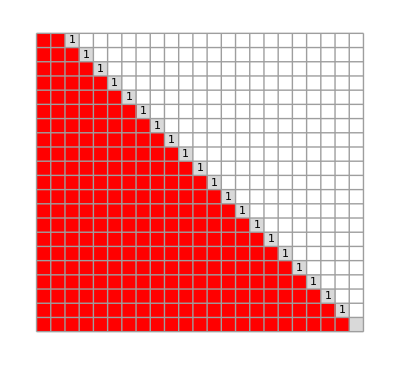
-Graphics- | → | -Graphics-Substitution Rule:
 
-Graphics-

```mathematica
myListLook[4]
```

```mathematica
SSS[{"B"->"ABAA"},"CBC",20]
```

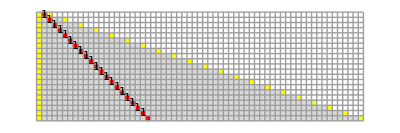

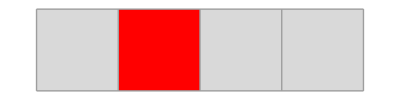
```mathematica
{{-Graphics-}, {" "}, {{{-Graphics-, "→", -Graphics-}}"Substitution Rule:"}}
```

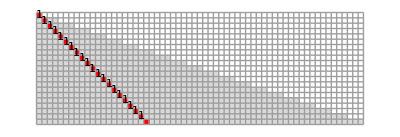
```mathematica
{{-Graphics-}, {" "}, {{{-Graphics-, "→", -Graphics-}}"Substitution Rule:"}}
```

```mathematica
SSS[{"AA"->"A",""->"ABAAA"},"C",20]
```

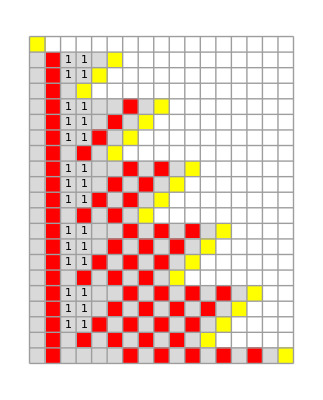
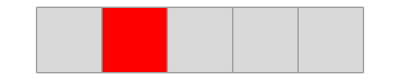
```mathematica
{{-Graphics-}, {" "}, {{{-Graphics-, "→", -Graphics-}, {-Graphics-, "→", -Graphics-}}"Substitution Rules:"}}
```

```mathematica
SSS[{"A"->"BA"},"CAC",20]
```

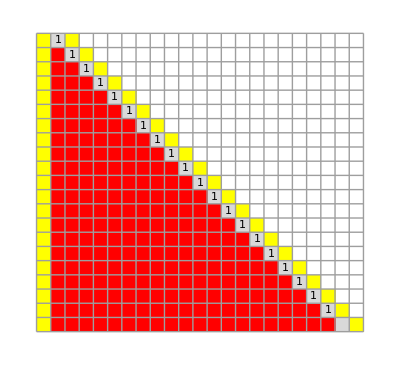
```mathematica
{{-Graphics-}, {" "}, {{{-Graphics-, "→", -Graphics-}}"Substitution Rule:"}}
```

```mathematica
SSS[{"A"->"AB"},"CAC",20]
```

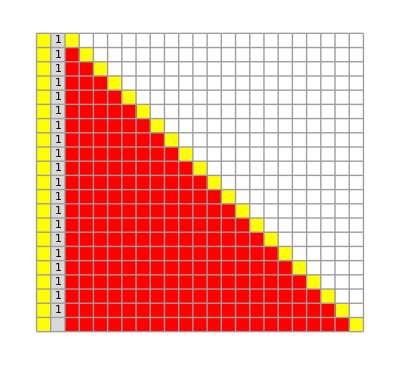

```mathematica
{{-Graphics-}, {" "}, {{{-Graphics-, "→", -Graphics-}}"Substitution Rule:"}}
```

```mathematica
SSS[{""->"A"},"C",20]
```

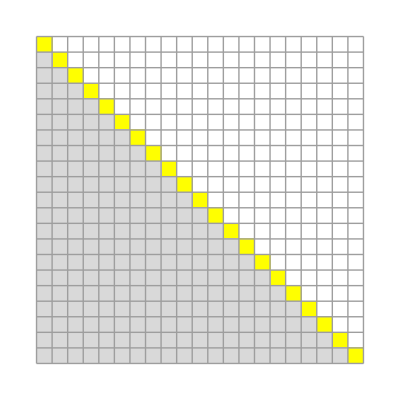
```mathematica
{{-Graphics-}, {" "}, {{{-Graphics-, "→", -Graphics-}}"Substitution Rule:"}}
```

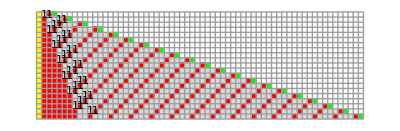
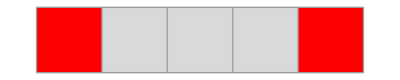
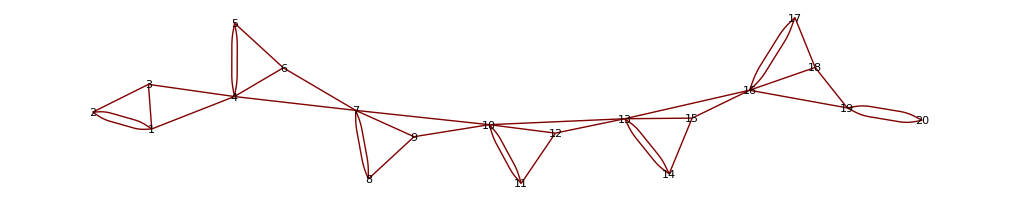
-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
SSS[{"AB"->"BAAAB"},"CABD",20]
```